```mathematica
(*Define constants of the problem*)
kBT=1.380649*10^(-23) * 200 * 10^-9;
a0=5.29*10^(-11);
hPlanck=6.62607015*10^(-34);
hbar=hPlanck/(2*Pi);
muNa40K=14.594251717637002*1.660538782*10^(-27);
ai=-2831.85 * a0;
af=9.82 * a0;
(*energies in units of kBT*)
Ei=hbar^2/(2*muNa40K*ai^2) / kBT;
Ef=hbar^2/(2*muNa40K*af^2) / kBT;
```

```mathematica
(*Lineshape from first-order calculation*)
```

```mathematica
Lineshape[rf_,Ek_]:=(Sqrt[Ek]/(1+Ek/Ei))*(1/(1+(rf+Ek)/Ef))*(Sqrt[rf+Ek]/(rf^2))*(ai-af)^2
```

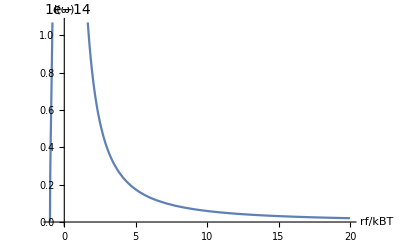

```mathematica
Plot[Lineshape[rf,1],{rf,-10,20},PlotRange->Automatic, AxesLabel->{"rf/kBT","I(ω)"}]
```

```mathematica
ConvolvedLineshape[rf_]:=NIntegrate[Lineshape[rf,Ek]*Exp[-Ek],{Ek,0,2}];
```

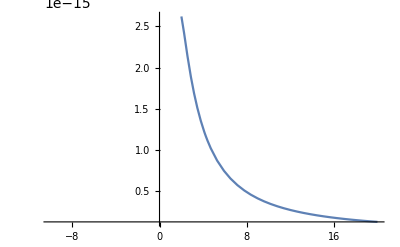

```mathematica
Plot[ConvolvedLineshape[rf],{rf,-10,20},PlotRange->Full]
```

```mathematica
(1/(2*Pi))*(h*OR^2)*Integrate[Sqrt[e*EM]/((e+EM)^2*e*(En-e)),{e,0,Infinity},PrincipalValue->True]
```

ConditionalExpression[((3 EM+En) h OR^2)/(4 EM (EM+En)^2), Im[En]==0&&(Im[EM]≠0||Re[EM]≥0)&&Re[En]>0]

```mathematica
(*Threshold function convolved with Blackman envelope*)
```

```mathematica
Thres[rf_,Eb_]:=Sqrt[rf-Eb]/rf^2;
```

```mathematica
ConvoledDissociationLine[rf_]:=NIntegrate[Thres[rf,Eb]*PDF[NormalDistribution[100,10],Eb],{Eb,-100,100}]
```

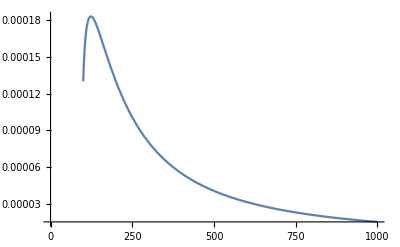

```mathematica
Plot[ConvoledDissociationLine[rf],{rf,0,1000},PlotRange->Full]
```

```mathematica
PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
A[w_]:=NIntegrate[k*Exp[-k^2/2]*k/((w - k^2)^2 + 0.5*k^2),{k,0,1000}]
```

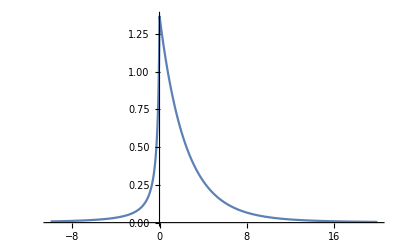

```mathematica
Plot[A[w],{w,-10,20},PlotRange->Full]
```

```mathematica
FullSimplify[Abs[(x1-I*y1)*(x2-I*y2)-a]^2,Assumptions->{x1>0,y1>0,x2>0,y2>0,a>0}]
```

(x2 y1+x1 y2)^2+(a-x1 x2+y1 y2)^2

```mathematica
FullSimplify[Abs[a+I*b]^2,Assumptions->{a>0,b>0}]
```

a^2+b^2

```mathematica
FullSimplify[Im[1/(a+I*b)],Assumptions->{a>0,b>0}]
```

Im[1/(a+ⅈ b)]

```mathematica
G[w_]:=1/(w-Ep-I*Su - Ω0^2/4 * 1/(w - Ep - Δ0-I*Sd));
```

```mathematica
ComplexExpand[1/(a-I*b)]
```

a/(a^2+b^2)+(ⅈ b)/(a^2+b^2)